```mathematica
<< IGraphM`
ParallelNeeds["IGraphM`"]

mot2 = IGShorthand[#, SelfLoops -> True, VertexLabels -> None, ImageSize -> Tiny, VertexSize -> Tiny] & /@
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

## V strength circuits

```mathematica
Vmat=Import["/Users/yingtongliu/Documents/research/CC-model_weight_mat/V_strength_mat.txt","Table"]
TableForm[Vmat]
```

{{	,G-MDSCs,M-MDSCs,Effector CD8+ T cells,Exhausted CD8+ T cells,Cancer,NKs},{G-MDSCs,0.866383,0.696283,0.481116,0.106481,0.0709425,0.0837365},{M-MDSCs,0.774814,0.626053,0.565064,0.102543,0.0665103,0.0703466},{Effector CD8+ T cells,0.514639,0.540888,1.5366,0.120377,0.293321,0.199388},{Exhausted CD8+ T cells,0.448319,0.480136,1.67038,0.172043,0.299004,0.26235},{Cancer,0.888885,0.803188,0.894941,0.353782,1.0929,0.376372},{NKs,0.473968,0.494323,1.20334,0.0842337,0.305095,0.193186}}

| G-MDSCs | M-MDSCs | Effector CD8+ T cells | Exhausted CD8+ T cells | Cancer | NKs
G-MDSCs | 0.866383 | 0.696283 | 0.481116 | 0.106481 | 0.0709425 | 0.0837365
M-MDSCs | 0.774814 | 0.626053 | 0.565064 | 0.102543 | 0.0665103 | 0.0703466
Effector CD8+ T cells | 0.514639 | 0.540888 | 1.5366 | 0.120377 | 0.293321 | 0.199388
Exhausted CD8+ T cells | 0.448319 | 0.480136 | 1.67038 | 0.172043 | 0.299004 | 0.26235
Cancer | 0.888885 | 0.803188 | 0.894941 | 0.353782 | 1.0929 | 0.376372
NKs | 0.473968 | 0.494323 | 1.20334 | 0.0842337 | 0.305095 | 0.193186

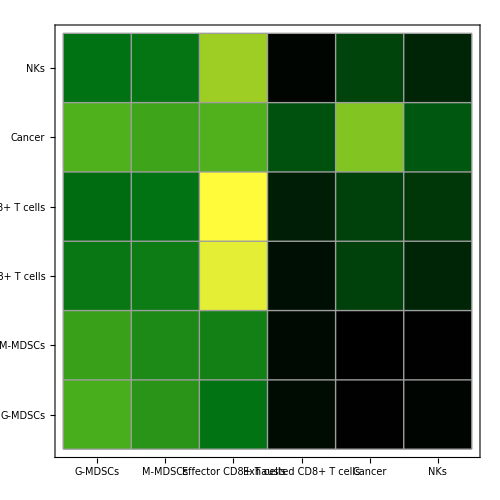
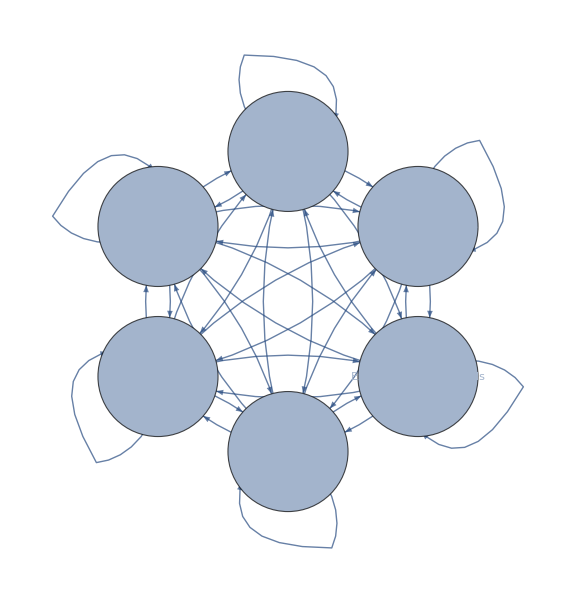

```mathematica
WVmat=Reverse@Rest@Union@Flatten@Vmat[[2;;,2;;]];
{
Row[{MatrixPlot[
Rescale@Vmat[[2;;,2;;]],
Mesh->True,PlotRangePadding->None,FrameTicks->{{{Range@6,Vmat[[1,2;;]]}ᵀ,None},{{Range@6,Rotate[#,π/2]&/@Vmat[[1,2;;]]}ᵀ,None}},ImageSize->500,ColorFunction->"AvocadoColors",ColorFunctionScaling->False,DataReversed->True],BarLegend[{"AvocadoColors",WVmat[[{-1,1}]]}]}],
Graph[
Rule@@Vmat[[1,#+1]]/.x_String:>StringReplace[x,"_"->"\n"]&/@Position[Vmat[[2;;,2;;]],_?(#>0&)],
VertexSize->.8,VertexLabels->Placed["Name",{.5,.5}],ImageSize->Large,GraphLayout->"CircularEmbedding"]}
```

```mathematica
ct=Vmat[[1,2;;]];
sr=Thread[ct->{"G-MDSCs","M-MDSCs","Eff CD8+T","Ex CD8+T","Cancer", "NKs"}];
```

```mathematica
indexPal=2*(Length@ReverseSort[DeleteCases[Flatten[Vmat⟦2;;,2;;⟧],0]])/3;
indexPal
```

24

```mathematica
TH=ReverseSort[DeleteCases[Flatten[Vmat⟦2;;,2;;⟧],0]][[indexPal]];
TH
```

0.293321

```mathematica
Total[ReverseSort[DeleteCases[Flatten[Vmat⟦2;;,2;;⟧],0]][[indexPal;;]]]/Total[ReverseSort[DeleteCases[Flatten[Vmat⟦2;;,2;;⟧],0]]]
```

0.100234

```mathematica
0.10023425026061318
```

0.100234

```mathematica
m=AdjacencyGraph[ct/.sr,UnitStep[Vmat[[2;;,2;;]]-TH]];
ws=Dispatch[Thread[Flatten[Outer[DirectedEdge,ct,ct]]->Flatten[Vmat[[2;;,2;;]]]]/.sr];
rootPal=MaximalBy[Vmat[[2;;]],Total@#[[2;;]]&][[1,1]];
```

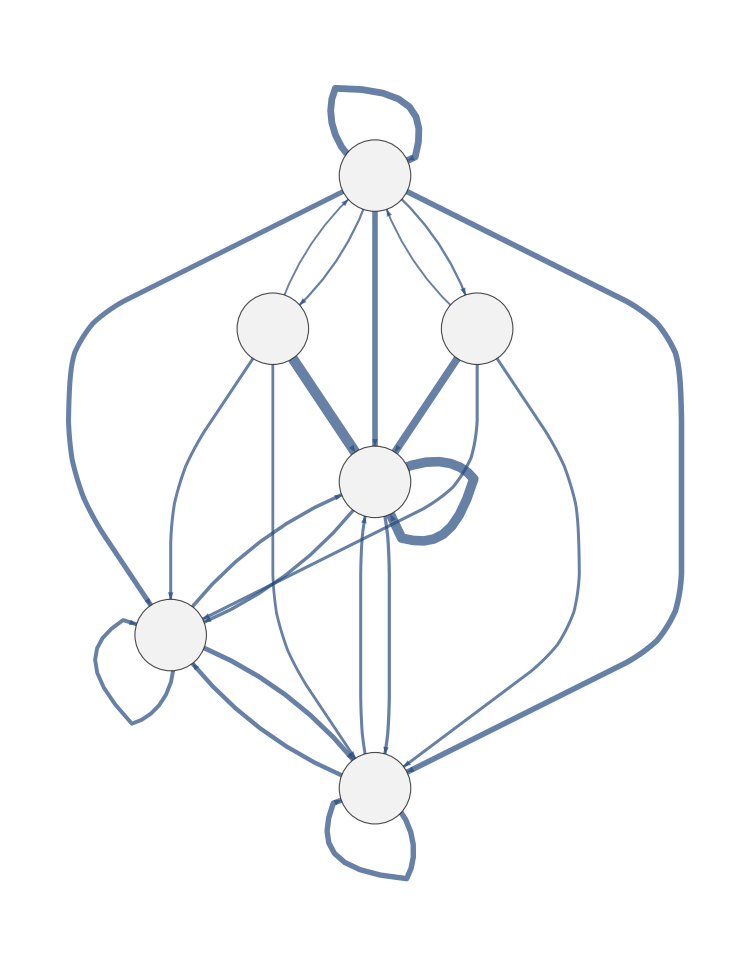

```mathematica
Graph[
#[[;;,1]],
EdgeStyle->Thread[#[[;;,1]]->(Thickness[#.01]&/@(#/(Max@#))&@#[[;;,2]])],
GraphLayout->{"LayeredDigraphEmbedding", "RootVertex"->rootPal},VertexSize->.7,VertexLabels->Placed["Name",{.5,.5}],ImageSize->750,AspectRatio->1,VertexLabels->Placed["Name",{0.5,0.5}],VertexSize->0.75,VertexStyle->GrayLevel[.95]]&@Select[Thread[Flatten[Outer[DirectedEdge,ct,ct]]->Flatten[Vmat[[2;;,2;;]]]]/.sr,#[[2]]>TH&]
```

```mathematica
real=Table[
Total[Mean[#/.ws]&/@(Union[Sort@EdgeList[Subgraph[m,#]]&/@(Normal/@IGLADFindSubisomorphisms[IGShorthand[c,SelfLoops->True],m,"Induced"->True])[[;;,;;,2]]])],
{c,{"1->2","2<->2<-1","1<->1->2","1<->1->2<->2","1->2->1","1<->1<->2","1<->1<->2<->2"}}];
```

```mathematica
rand=Through[{Mean,StandardDeviation}[#]]&/@(ParallelTable[
Module[{rg,ws},
rg=IGRewire[m,10000,SelfLoops->True];
ws=Dispatch[Thread[EdgeList[rg]->RandomSample[WVmat[[;;indexPal]]]]];
Table[
Total[Mean[#/.ws]&/@(Union[Sort@EdgeList[Subgraph[rg,#]]&/@(Normal/@IGLADFindSubisomorphisms[IGShorthand[c,SelfLoops->True],rg,"Induced"->True])[[;;,;;,2]]])],
{c,{"1->2","2<->2<-1","1<->1->2","1<->1->2<->2","1->2->1","1<->1<->2","1<->1<->2<->2"}}
]
],
10^4]ᵀ);
```

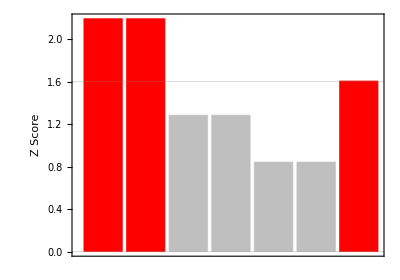

```mathematica
BarChart[Style[#,If[#>1.6,Red,GrayLevel[.75]]]&/@((real-rand[[;;,1]])/rand[[;;,2]]),ChartLabels->(Rotate[#,π/2]&/@mot2),PlotRange->All,Frame->True,GridLines->{None,{0,1.6}},FrameLabel->{None,"Z Score"},AspectRatio->.7,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,14]]
```

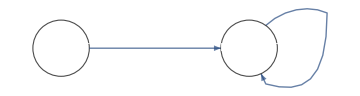
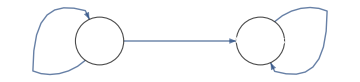
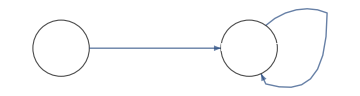
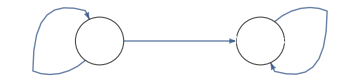
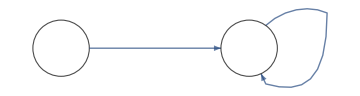
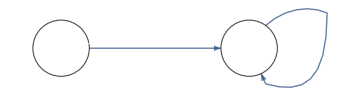
-Graphics-Interaction | Weight
Ex CD8+T->Eff CD8+T | 1.67038
Eff CD8+T->Eff CD8+T | 1.5366
Total | 3.20698
-Graphics-Interaction | Weight
Cancer->Cancer | 1.0929
Cancer->G-MDSCs | 0.888885
G-MDSCs->G-MDSCs | 0.866383
Total | 2.84817
-Graphics-Interaction | Weight
Eff CD8+T->Eff CD8+T | 1.5366
NKs->Eff CD8+T | 1.20334
Total | 2.73995
-Graphics-Interaction | Weight
Cancer->Cancer | 1.0929
Cancer->M-MDSCs | 0.803188
M-MDSCs->M-MDSCs | 0.626053
Total | 2.52214
-Graphics-Interaction | Weight
G-MDSCs->G-MDSCs | 0.866383
NKs->G-MDSCs | 0.473968
Total | 1.34035
-Graphics-Interaction | Weight
G-MDSCs->G-MDSCs | 0.866383
Ex CD8+T->G-MDSCs | 0.448319
Total | 1.3147
-Graphics-Interaction | Weight
M-MDSCs->M-MDSCs | 0.626053
NKs->M-MDSCs | 0.494323
Total | 1.12038
-Graphics-Interaction | Weight
M-MDSCs->M-MDSCs | 0.626053
Ex CD8+T->M-MDSCs | 0.480136
Total | 1.10619

```mathematica
Column[
Row[Most[#1]/.{DirectedEdge[y_,z_]:>Style[(y<>"->"<>z)],x_String:>StringReplace[x,"_"->" "]},Spacer@10,Alignment->Center]&/@ReverseSortBy[
Union[(Flatten[({
Graph[
EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}],VertexLabels->Placed["Name",{0.5,0.5}],VertexSize->0.3,VertexStyle->White,ImageSize->Medium,EdgeStyle->Thread[(EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}])->((Thickness[#.015]&/@(#/(Max@#)))&@(EdgeList@#1/.ws))],VertexStyle->GrayLevel@.9,VertexCoordinates->{{0,0},{1,0}}],({TableForm[Join[ReverseSortBy[Transpose[{#1,#1/.ws}],Last],{Style[#,Bold]&/@{"Total",Tr[#1/.ws]}(*,{"Mean",Mean[#1/.ws]}*)}],TableHeadings->{None,{"Interaction","Weight"}}],Tr[#1/.ws]}&)[EdgeList[#1]]}&)[Subgraph[m,#1]]]&)/@(Normal/@IGLADFindSubisomorphisms[IGShorthand["1->2",SelfLoops->True],m,"Induced"->True])⟦1;;All,1;;All,2⟧,SameTest->(#1⟦-1⟧==#2⟦-1⟧&)],Last]
]
```

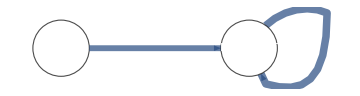
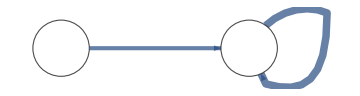
{{-Graphics-,Interaction | Weight
Eff CD8+T->Eff CD8+T | 1.5366
NKs->Eff CD8+T | 1.20334
Total | 2.73995,2.73995},{-Graphics-,Interaction | Weight
G-MDSCs->G-MDSCs | 0.866383
NKs->G-MDSCs | 0.473968
Total | 1.34035,1.34035}}

```mathematica
Union[(Flatten[({
Graph[
EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}],VertexLabels->Placed["Name",{0.5,0.5}],VertexSize->0.3,VertexStyle->White,ImageSize->Medium,EdgeStyle->Thread[(EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}])->((Thickness[#.015]&/@(#/(Max@#)))&@(EdgeList@#1/.ws))],VertexStyle->GrayLevel@.9,VertexCoordinates->{{0,0},{1,0}}],({TableForm[Join[ReverseSortBy[Transpose[{#1,#1/.ws}],Last],{Style[#,Bold]&/@{"Total",Tr[#1/.ws]}(*,{"Mean",Mean[#1/.ws]}*)}],TableHeadings->{None,{"Interaction","Weight"}}],Tr[#1/.ws]}&)[EdgeList[#1]]}&)[Subgraph[m,#1]]]&)/@(Normal/@IGLADFindSubisomorphisms[IGShorthand["1->2",SelfLoops->True],m,"Induced"->True])⟦6;;7,1;;All,2⟧,SameTest->(#1⟦-1⟧==#2⟦-1⟧&)]
```

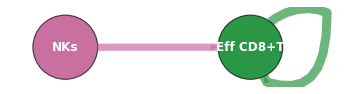

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{"NKs" -> "Eff CD8+T", "Eff CD8+T"-> "Eff CD8+T"}, VertexLabels->Placed["Name",{0.5,0.5}],VertexSize->0.35,VertexLabelStyle-> Directive[White,Bold, 12],VertexStyle->{"NKs"-> RGBColor["#c970a1"], "Eff CD8+T"-> RGBColor["#2b9746"]},EdgeStyle->{("NKs"->"Eff CD8+T")-> Directive[Thickness[1.2 * 0.012],RGBColor["#c970a1"]], 
("Eff CD8+T"->"Eff CD8+T")-> Directive[Thickness[1.5 * 0.012],RGBColor["#2b9746"]], Arrowheads[Large]},
ImageSize->Medium, VertexStyle->GrayLevel@.9,VertexCoordinates->{{0,0},{1,0}}]
```

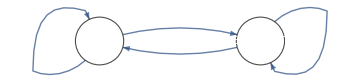
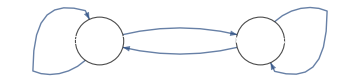
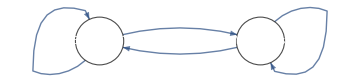
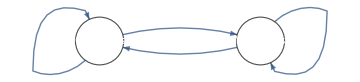
-Graphics-Interaction | Weight
Eff CD8+T->Eff CD8+T | 1.5366
Cancer->Cancer | 1.0929
Cancer->Eff CD8+T | 0.894941
Eff CD8+T->Cancer | 0.293321
Total | 3.81777
-Graphics-Interaction | Weight
Eff CD8+T->Eff CD8+T | 1.5366
G-MDSCs->G-MDSCs | 0.866383
Eff CD8+T->G-MDSCs | 0.514639
G-MDSCs->Eff CD8+T | 0.481116
Total | 3.39874
-Graphics-Interaction | Weight
Eff CD8+T->Eff CD8+T | 1.5366
M-MDSCs->M-MDSCs | 0.626053
M-MDSCs->Eff CD8+T | 0.565064
Eff CD8+T->M-MDSCs | 0.540888
Total | 3.26861
-Graphics-Interaction | Weight
G-MDSCs->G-MDSCs | 0.866383
M-MDSCs->G-MDSCs | 0.774814
G-MDSCs->M-MDSCs | 0.696283
M-MDSCs->M-MDSCs | 0.626053
Total | 2.96353

```mathematica
Column[
Row[Most[#1]/.{DirectedEdge[y_,z_]:>Style[(y<>"->"<>z)],x_String:>StringReplace[x,"_"->" "]},Spacer@10,Alignment->Center]&/@ReverseSortBy[
Union[(Flatten[({
Graph[
EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}],VertexLabels->Placed["Name",{0.5,0.5}],VertexSize->0.3,VertexStyle->White,ImageSize->Medium,EdgeStyle->Thread[(EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}])->((Thickness[#.015]&/@(#/(Max@#)))&@(EdgeList@#1/.ws))],VertexStyle->GrayLevel@.9,VertexCoordinates->{{0,0},{1,0}}],({TableForm[Join[ReverseSortBy[Transpose[{#1,#1/.ws}],Last],{Style[#,Bold]&/@{"Total",Tr[#1/.ws]}(*,{"Mean",Mean[#1/.ws]}*)}],TableHeadings->{None,{"Interaction","Weight"}}],Tr[#1/.ws]}&)[EdgeList[#1]]}&)[Subgraph[m,#1]]]&)/@(Normal/@IGLADFindSubisomorphisms[IGShorthand["1<->1<->2<->2",SelfLoops->True],m,"Induced"->True])⟦1;;All,1;;All,2⟧,SameTest->(#1⟦-1⟧==#2⟦-1⟧&)],Last]
]
```

### 3-node motif

```mathematica
mot3={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
real3=Table[
Total[Mean[#/.ws]&/@(Union[Sort@EdgeList[Subgraph[m,#]]&/@(Normal/@IGLADFindSubisomorphisms[c,m,"Induced"->True])[[;;,;;,2]]])],
{c,Delete[mot3,{{4},{2},{1}}]}]
```

{2.59984,0,0,0,0,5.62166,0,0.485431,0,0,2.55098,3.30715,0.733538}

```mathematica
rand3=Through[{Mean,StandardDeviation}[#]]&/@(ParallelTable[
Module[{rg,ws},
rg=IGRewire[m,10000,SelfLoops->True];
ws=Dispatch[Thread[EdgeList[rg]->RandomSample[WVmat[[;;indexPal]]]]];
Table[
Total[Mean[#/.ws]&/@(Union[Sort@EdgeList[Subgraph[rg,#]]&/@(Normal/@IGLADFindSubisomorphisms[c,rg,"Induced"->True])[[;;,;;,2]]])],
{c,Delete[mot3,{{4},{2},{1}}]}
]
],
10^4]ᵀ)
```

{{2.07953,0.292801},{0,0},{0,0},{0,0},{0,0},{4.86752,0.428144},{0,0},{0.692424,0.147204},{0,0},{0,0},{2.77198,0.331651},{2.78079,0.316461},{0.697355,0.0975467}}

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

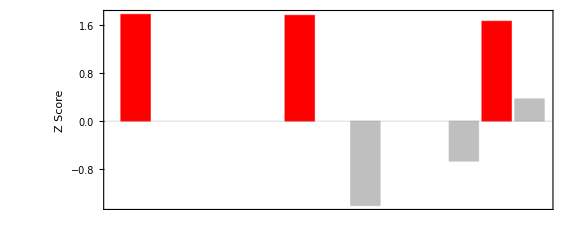

```mathematica
BarChart[Style[#,If[#>1.6,Red,GrayLevel[.75]]]&/@((real3-rand3[[;;,1]])/rand3[[;;,2]]),ChartLabels->Delete[mot3,{{4},{2},{1}}],PlotRange->All,Frame->True,GridLines->{None,{0}},FrameLabel->{None,"Z Score"},AspectRatio->.4,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,14], ImageSize->Large]
```

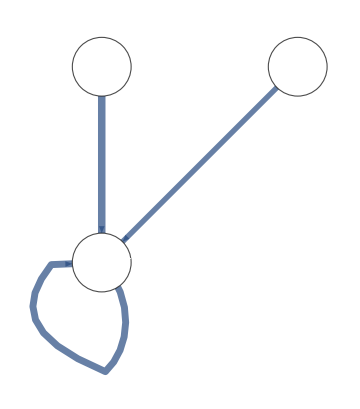
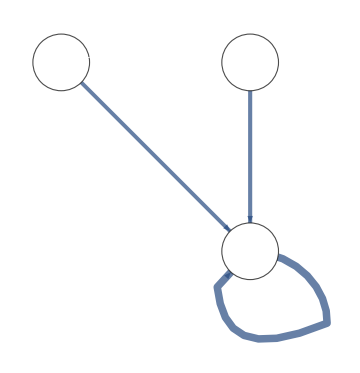
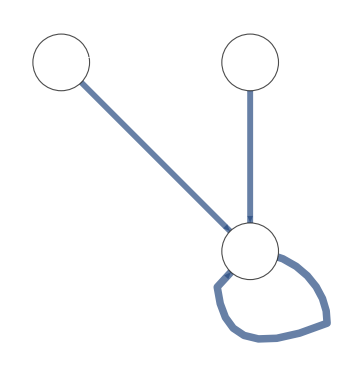
-Graphics-
Interaction | Weight
Ex CD8+T->Eff CD8+T | 1.67038
Eff CD8+T->Eff CD8+T | 1.5366
NKs->Eff CD8+T | 1.20334
Total | 4.41032 | -Graphics-
Interaction | Weight
G-MDSCs->G-MDSCs | 0.866383
NKs->G-MDSCs | 0.473968
Ex CD8+T->G-MDSCs | 0.448319
Total | 1.78867 | -Graphics-
Interaction | Weight
M-MDSCs->M-MDSCs | 0.626053
NKs->M-MDSCs | 0.494323
Ex CD8+T->M-MDSCs | 0.480136
Total | 1.60051

```mathematica
Grid@Partition[
Column[Most@Flatten[({
Graph[
EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}],VertexLabels->Placed["Name",{0.5,0.5}],VertexSize->0.3,VertexStyle->White,ImageSize->Medium,EdgeStyle->Thread[(EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}])->((Thickness[#.015]&/@(#/(Max@#)))&@(EdgeList@#1/.ws))]],({TableForm[Join[ReverseSortBy[Transpose[{#1,#1/.ws}],Last],{Style[#,Bold]&/@{"Total",Tr[#1/.ws]}}],TableHeadings->{None,{"Interaction","Weight"}}],Tr[#1/.ws]}&)[#]})],
Alignment->Center]&/@ReverseSortBy[
Union[Sort@EdgeList[Subgraph[m,#]]&/@(Normal/@IGLADFindSubisomorphisms[mot3[[3]],m,"Induced"->True])[[;;,;;,2]]],
Total[#/.ws]&
],
UpTo@3]/.x_String:>StringReplace[x,"\n"->" "]
```

```mathematica
{{□, , }, {, , }, {, , }}
```

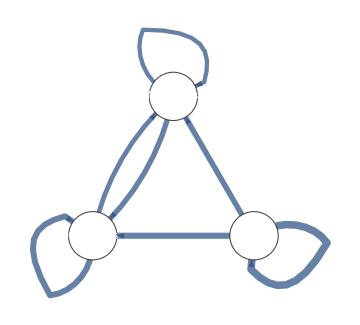
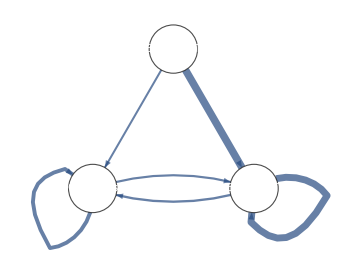
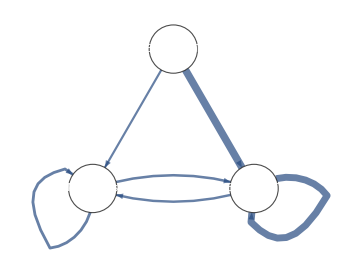
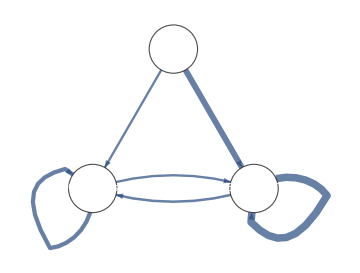
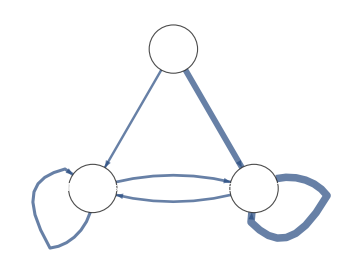
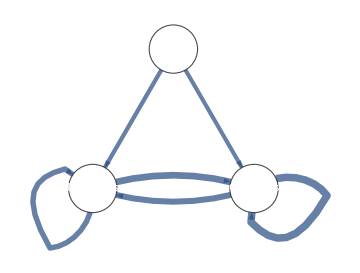
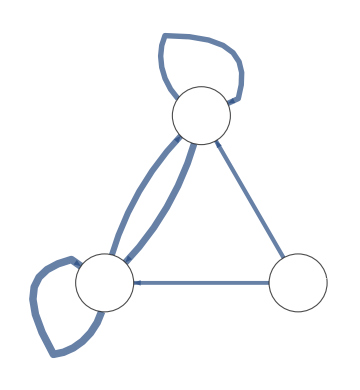
-Graphics-
Interaction | Weight
Cancer->Cancer | 1.0929
Cancer->G-MDSCs | 0.888885
G-MDSCs->G-MDSCs | 0.866383
Cancer->M-MDSCs | 0.803188
M-MDSCs->G-MDSCs | 0.774814
G-MDSCs->M-MDSCs | 0.696283
M-MDSCs->M-MDSCs | 0.626053
Total | 5.74851 | -Graphics-
Interaction | Weight
Ex CD8+T->Eff CD8+T | 1.67038
Eff CD8+T->Eff CD8+T | 1.5366
G-MDSCs->G-MDSCs | 0.866383
Eff CD8+T->G-MDSCs | 0.514639
G-MDSCs->Eff CD8+T | 0.481116
Ex CD8+T->G-MDSCs | 0.448319
Total | 5.51744 | -Graphics-
Interaction | Weight
Ex CD8+T->Eff CD8+T | 1.67038
Eff CD8+T->Eff CD8+T | 1.5366
M-MDSCs->M-MDSCs | 0.626053
M-MDSCs->Eff CD8+T | 0.565064
Eff CD8+T->M-MDSCs | 0.540888
Ex CD8+T->M-MDSCs | 0.480136
Total | 5.41912
-Graphics-
Interaction | Weight
Eff CD8+T->Eff CD8+T | 1.5366
NKs->Eff CD8+T | 1.20334
G-MDSCs->G-MDSCs | 0.866383
Eff CD8+T->G-MDSCs | 0.514639
G-MDSCs->Eff CD8+T | 0.481116
NKs->G-MDSCs | 0.473968
Total | 5.07605 | -Graphics-
Interaction | Weight
Eff CD8+T->Eff CD8+T | 1.5366
NKs->Eff CD8+T | 1.20334
M-MDSCs->M-MDSCs | 0.626053
M-MDSCs->Eff CD8+T | 0.565064
Eff CD8+T->M-MDSCs | 0.540888
NKs->M-MDSCs | 0.494323
Total | 4.96627 | -Graphics-
Interaction | Weight
G-MDSCs->G-MDSCs | 0.866383
M-MDSCs->G-MDSCs | 0.774814
G-MDSCs->M-MDSCs | 0.696283
M-MDSCs->M-MDSCs | 0.626053
NKs->M-MDSCs | 0.494323
NKs->G-MDSCs | 0.473968
Total | 3.93182
-Graphics-
Interaction | Weight
G-MDSCs->G-MDSCs | 0.866383
M-MDSCs->G-MDSCs | 0.774814
G-MDSCs->M-MDSCs | 0.696283
M-MDSCs->M-MDSCs | 0.626053
Ex CD8+T->M-MDSCs | 0.480136
Ex CD8+T->G-MDSCs | 0.448319
Total | 3.89199 |  |

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Grid@Partition[Column[Most@Flatten[({Graph[EdgeList[#1]/. x_String:>StringReplace[x,{"_"->" ","/"->"\n"}],VertexLabels->Placed["Name",{0.5,0.5}],VertexSize->0.3,VertexStyle->White,ImageSize->Medium,GraphLayout->{"Dimension"->2},(*Add manual layout*)VertexCoordinates->{{Sqrt[3]/2,-1},{-1/2*Sqrt[3],-1},{0,1/2}},(*Inverted triangle layout*)EdgeStyle->Thread[(EdgeList[#1]/. x_String:>StringReplace[x,{"_"->" ","/"->"\n"}])->((Thickness[# .015]&/@(#/Max@#))&@(EdgeList@#1/. ws))]],({TableForm[Join[ReverseSortBy[Transpose[{#1,#1/. ws}],Last],{Style[#,Bold]&/@{"Total",Tr[#1/. ws]}}],TableHeadings->{None,{"Interaction","Weight"}}],Tr[#1/. ws]}&)[#]})],Alignment->Center]&/@ReverseSortBy[Union[Sort@EdgeList[Subgraph[m,#]]&/@(Normal/@IGLADFindSubisomorphisms[mot3[[9]],m,"Induced"->True])[[;;,;;,2]]],Total[#/. ws]&],UpTo@3]/. x_String:>StringReplace[x,"\n"->" "]
```

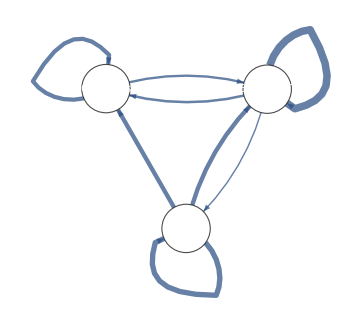
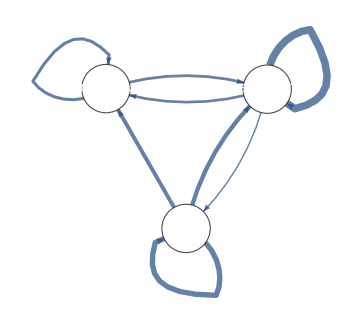
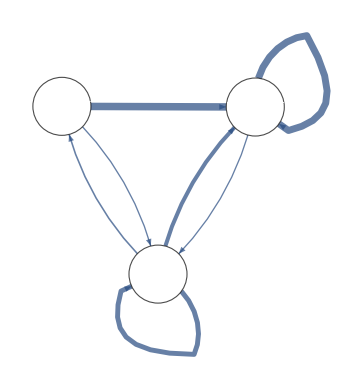
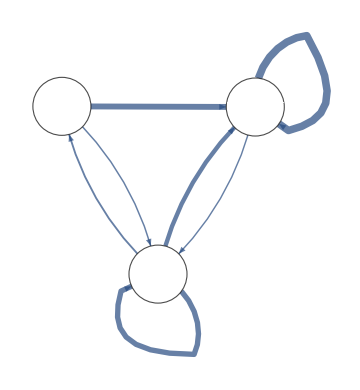
-Graphics-
Interaction | Weight
Eff CD8+T->Eff CD8+T | 1.5366
Cancer->Cancer | 1.0929
Cancer->Eff CD8+T | 0.894941
Cancer->G-MDSCs | 0.888885
G-MDSCs->G-MDSCs | 0.866383
Eff CD8+T->G-MDSCs | 0.514639
G-MDSCs->Eff CD8+T | 0.481116
Eff CD8+T->Cancer | 0.293321
Total | 6.56879 | -Graphics-
Interaction | Weight
Eff CD8+T->Eff CD8+T | 1.5366
Cancer->Cancer | 1.0929
Cancer->Eff CD8+T | 0.894941
Cancer->M-MDSCs | 0.803188
M-MDSCs->M-MDSCs | 0.626053
M-MDSCs->Eff CD8+T | 0.565064
Eff CD8+T->M-MDSCs | 0.540888
Eff CD8+T->Cancer | 0.293321
Total | 6.35296 | -Graphics-
Interaction | Weight
Ex CD8+T->Eff CD8+T | 1.67038
Eff CD8+T->Eff CD8+T | 1.5366
Cancer->Cancer | 1.0929
Cancer->Eff CD8+T | 0.894941
Cancer->Ex CD8+T | 0.353782
Ex CD8+T->Cancer | 0.299004
Eff CD8+T->Cancer | 0.293321
Total | 6.14093
-Graphics-
Interaction | Weight
Eff CD8+T->Eff CD8+T | 1.5366
NKs->Eff CD8+T | 1.20334
Cancer->Cancer | 1.0929
Cancer->Eff CD8+T | 0.894941
Cancer->NKs | 0.376372
NKs->Cancer | 0.305095
Eff CD8+T->Cancer | 0.293321
Total | 5.70258 |  |

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Grid@Partition[
Column[Most@Flatten[({
Graph[
EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}],VertexLabels->Placed["Name",{0.5,0.5}],VertexSize->0.3,VertexStyle->White,ImageSize->Medium,EdgeStyle->Thread[(EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}])->((Thickness[#.015]&/@(#/(Max@#)))&@(EdgeList@#1/.ws))]],({TableForm[Join[ReverseSortBy[Transpose[{#1,#1/.ws}],Last],{Style[#,Bold]&/@{"Total",Tr[#1/.ws]}}],TableHeadings->{None,{"Interaction","Weight"}}],Tr[#1/.ws]}&)[#]})],
Alignment->Center]&/@ReverseSortBy[
Union[Sort@EdgeList[Subgraph[m,#]]&/@(Normal/@IGLADFindSubisomorphisms[mot3[[15]],m,"Induced"->True])[[;;,;;,2]]],
Total[#/.ws]&
],
UpTo@3]/.x_String:>StringReplace[x,"\n"->" "]
```

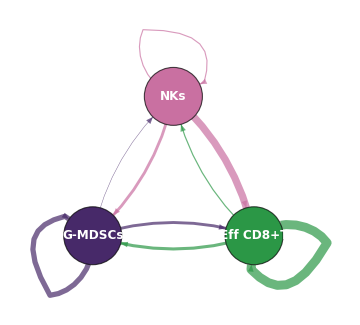

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{1,2,3},{1->1, 1->2, 1->3,2->1,2->2, 2->3,3->1, 3->2, 3-> 3},{FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},ImageSize->Medium,VertexCoordinates->{{-1/2*Sqrt[3],-1}, {0,1/2},{Sqrt[3]/2,-1}},VertexLabels->Thread[Range[3]->(Placed[Style[#,12,"Panel",Background->None, Bold, White], Center]&/@{ "G-MDSCs",  "NKs","Eff CD8+T"})],
VertexStyle->{2-> RGBColor["#c970a1"], 1 -> RGBColor["#472969"],3-> RGBColor["#2b9746"]},EdgeStyle->{
(1->1) -> Directive[Thickness[0.87 * 0.012],RGBColor["#472969"]],
(1->2) -> Directive[Thickness[0.08 * 0.012],RGBColor["#472969"]],
(1 -> 3)->  Directive[Thickness[0.48* 0.012],RGBColor["#472969"]],
(2 -> 1)-> Directive[Thickness[0.47 * 0.012],RGBColor["#c970a1"]],
(2->2)-> Directive[Thickness[ 0.19* 0.012],RGBColor["#c970a1"]], 
(2->3)-> Directive[Thickness[1.2 * 0.012],RGBColor["#c970a1"]], 
(3 -> 1)-> Directive[Thickness[0.51* 0.012],RGBColor["#2b9746"]],
(3 -> 2)-> Directive[Thickness[0.2 * 0.012],RGBColor["#2b9746"]],
(3->3)-> Directive[Thickness[1.5 * 0.012],RGBColor["#2b9746"]],  Arrowheads[Large]},
VertexSize->{0.36}}]
```

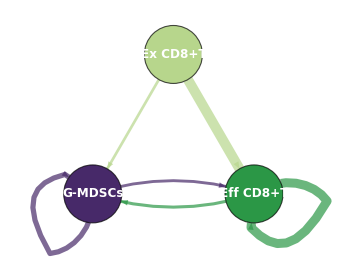

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{1,2,3},{1->3,2->1,2->3,3->1, 1->1, 3-> 3},{FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},ImageSize->Medium,VertexCoordinates->{{-1/2*Sqrt[3],-1}, {0,1/2},{Sqrt[3]/2,-1}},VertexLabels->Thread[Range[3]->(Placed[Style[#,12,"Panel",Background->None, Bold, White], Center]&/@{ "G-MDSCs",  "Ex CD8+T","Eff CD8+T"})],
VertexStyle->{2-> RGBColor["#b7d68c"], 1 -> RGBColor["#472969"],3-> RGBColor["#2b9746"]},EdgeStyle->{(2->3)-> Directive[Thickness[1.67 * 0.012],RGBColor["#b7d68c"]], 
(2 -> 1)-> Directive[Thickness[0.448 * 0.012],RGBColor["#b7d68c"]],
(1->1) -> Directive[Thickness[0.866 * 0.012],RGBColor["#472969"]],
(1 -> 3)->  Directive[Thickness[0.48* 0.012],RGBColor["#472969"]],
(3 -> 1)-> Directive[Thickness[0.51* 0.012],RGBColor["#2b9746"]],
(3->3)-> Directive[Thickness[1.5 * 0.012],RGBColor["#2b9746"]],  Arrowheads[Large]},
VertexSize->{0.36}}]
```

## E strength circuits

```mathematica
Emat=Import["/Users/yingtongliu/Documents/research/CC-model_weight_mat/E_strength_mat.txt","Table"]
TableForm[Emat]
```

{{	,G-MDSCs,M-MDSCs,Effector CD8+ T cells,Exhausted CD8+ T cells,Cancer,NKs},{G-MDSCs,0.790327,0.594673,0.156462,0.251547,0.0659814,0.0690055},{M-MDSCs,0.772089,0.623798,0.215995,0.32998,0.105911,0.11954},{Effector CD8+ T cells,0.429773,0.440743,0.385765,0.5356,0.310429,0.169239},{Exhausted CD8+ T cells,0.458173,0.463443,0.37871,0.536049,0.315011,0.177594},{Cancer,0.95102,0.930156,0.455158,0.804717,1.76202,0.236709},{NKs,0.414073,0.437197,0.282515,0.440333,0.33136,0.108342}}

| G-MDSCs | M-MDSCs | Effector CD8+ T cells | Exhausted CD8+ T cells | Cancer | NKs
G-MDSCs | 0.790327 | 0.594673 | 0.156462 | 0.251547 | 0.0659814 | 0.0690055
M-MDSCs | 0.772089 | 0.623798 | 0.215995 | 0.32998 | 0.105911 | 0.11954
Effector CD8+ T cells | 0.429773 | 0.440743 | 0.385765 | 0.5356 | 0.310429 | 0.169239
Exhausted CD8+ T cells | 0.458173 | 0.463443 | 0.37871 | 0.536049 | 0.315011 | 0.177594
Cancer | 0.95102 | 0.930156 | 0.455158 | 0.804717 | 1.76202 | 0.236709
NKs | 0.414073 | 0.437197 | 0.282515 | 0.440333 | 0.33136 | 0.108342

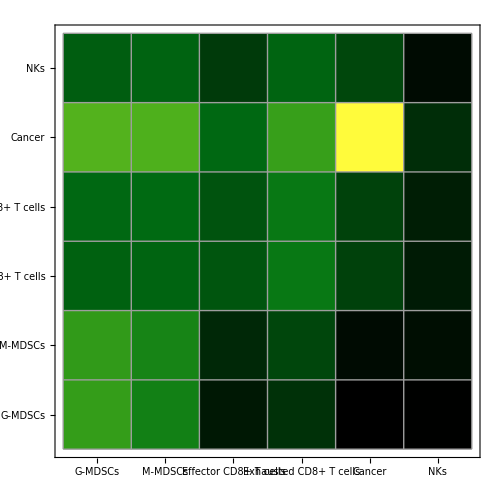
{-Graphics-,-Graphics-}

```mathematica
WEmat=Reverse@Rest@Union@Flatten@Emat[[2;;,2;;]];
{
Row[{MatrixPlot[
Rescale@Emat[[2;;,2;;]],
Mesh->True,PlotRangePadding->None,FrameTicks->{{{Range@6,Emat[[1,2;;]]}ᵀ,None},{{Range@6,Rotate[#,π/2]&/@Emat[[1,2;;]]}ᵀ,None}},ImageSize->500,ColorFunction->"AvocadoColors",ColorFunctionScaling->False,DataReversed->True],BarLegend[{"AvocadoColors",WEmat[[{-1,1}]]}]}],
Graph[
Rule@@Emat[[1,#+1]]/.x_String:>StringReplace[x,"_"->"\n"]&/@Position[Emat[[2;;,2;;]],_?(#>0&)],
VertexSize->.8,VertexLabels->Placed["Name",{.5,.5}],ImageSize->Large,GraphLayout->"CircularEmbedding"]}
```

```mathematica
ct=Emat[[1,2;;]];
sr=Thread[ct->{"G-MDSCs","M-MDSCs","Eff CD8+T","Ex CD8+T","Cancer", "NKs"}]
```

{G-MDSCs→G-MDSCs,M-MDSCs→M-MDSCs,Effector CD8+ T cells→Eff CD8+T,Exhausted CD8+ T cells→Ex CD8+T,Cancer→Cancer,NKs→NKs}

```mathematica
indexPal=2*(Length@ReverseSort[DeleteCases[Flatten[Emat⟦2;;,2;;⟧],0]])/3;
indexPal
```

24

```mathematica
TH=ReverseSort[DeleteCases[Flatten[Emat⟦2;;,2;;⟧],0]][[indexPal]];
TH
```

0.310429

```mathematica
Total[ReverseSort[DeleteCases[Flatten[Emat⟦2;;,2;;⟧],0]][[indexPal;;]]]/Total[ReverseSort[DeleteCases[Flatten[Emat⟦2;;,2;;⟧],0]]]
```

0.143177

```mathematica
Graph[Range@10,{1->1}]
```

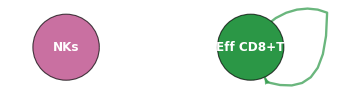

-Graphics-

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
g1 = Graph[{1, 2},{1->2,2-> 2}, VertexLabels->Thread[Range[2]->(Placed[Style[#,12,"Panel",Background->None, Bold, White], Center]&/@{ "NKs","Eff CD8+T"})],VertexSize->0.36,VertexLabelStyle-> Directive[White,Bold, 12],VertexStyle->{1-> RGBColor["#c970a1"], 2-> RGBColor["#2b9746"]},EdgeStyle->{(1 -> 2)-> Directive[Thickness[0.00012], White],(2 -> 2)-> Directive[Thickness[0.39 * 0.012],RGBColor["#2b9746"]], Arrowheads[Large]},ImageSize->Medium, VertexStyle->GrayLevel@.9,VertexCoordinates->{{0,0},{1,0}}]
g1
```

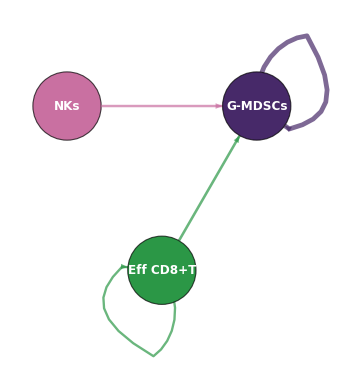

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{1,2,3},{2->1,3->1, 1->1, 3-> 3},{FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},ImageSize->Medium,VertexCoordinates->{{Sqrt[3]/2,1},{-1/2*Sqrt[3],1},{0,-1/2}},VertexLabels->Thread[Range[3]->(Placed[Style[#,12,"Panel",Background->None, Bold, White], Center]&/@{ "G-MDSCs",  "NKs","Eff CD8+T"})],
VertexStyle->{2-> RGBColor["#c970a1"], 1 -> RGBColor["#472969"],3-> RGBColor["#2b9746"]},EdgeStyle->{(2 -> 1)-> Directive[Thickness[0.41 * 0.012],RGBColor["#c970a1"]],
(1->1) -> Directive[Thickness[0.79 * 0.012],RGBColor["#472969"]],
(3 -> 1)-> Directive[Thickness[0.43* 0.012],RGBColor["#2b9746"]],
(3->3)-> Directive[Thickness[0.39 * 0.012],RGBColor["#2b9746"]],  Arrowheads[Large]},
VertexSize->{0.36}}]
```

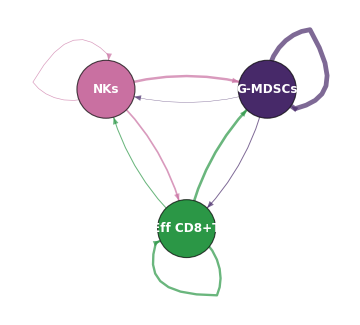

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{1,2,3},{1->1, 1->2, 1->3,2->1,2->2, 2->3,3->1, 3->2, 3-> 3},{FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},ImageSize->Medium,VertexCoordinates->{{Sqrt[3]/2,1},{-1/2*Sqrt[3],1},{0,-1/2}},VertexLabels->Thread[Range[3]->(Placed[Style[#,12,"Panel",Background->None, Bold, White], Center]&/@{ "G-MDSCs",  "NKs","Eff CD8+T"})],
VertexStyle->{2-> RGBColor["#c970a1"], 1 -> RGBColor["#472969"],3-> RGBColor["#2b9746"]},EdgeStyle->{
(1->1) -> Directive[Thickness[0.79 * 0.012],RGBColor["#472969"]],
(1->2) -> Directive[Thickness[ 0.07* 0.012],RGBColor["#472969"]],
(1 -> 3)->  Directive[Thickness[0.16 * 0.012],RGBColor["#472969"]],
(2 -> 1)-> Directive[Thickness[0.41 * 0.012],RGBColor["#c970a1"]],
(2->2)-> Directive[Thickness[0.11 * 0.012],RGBColor["#c970a1"]], 
(2->3)-> Directive[Thickness[ 0.28* 0.012],RGBColor["#c970a1"]], 
(3 -> 1)-> Directive[Thickness[0.43* 0.012],RGBColor["#2b9746"]],
(3 -> 2)-> Directive[Thickness[0.17 * 0.012],RGBColor["#2b9746"]],
(3->3)-> Directive[Thickness[0.39 * 0.012],RGBColor["#2b9746"]],  Arrowheads[Large]},
VertexSize->{0.36}}]
```

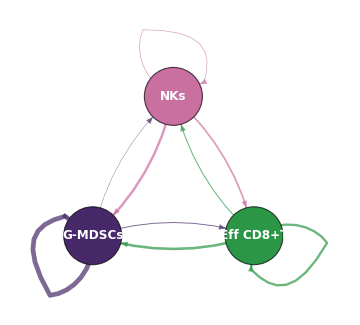

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{1,2,3},{1->1, 1->2, 1->3,2->1,2->2, 2->3,3->1, 3->2, 3-> 3},{FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},ImageSize->Medium,VertexCoordinates->{{-1/2*Sqrt[3],-1}, {0,1/2},{Sqrt[3]/2,-1}},VertexLabels->Thread[Range[3]->(Placed[Style[#,12,"Panel",Background->None, Bold, White], Center]&/@{ "G-MDSCs",  "NKs","Eff CD8+T"})],
VertexStyle->{2-> RGBColor["#c970a1"], 1 -> RGBColor["#472969"],3-> RGBColor["#2b9746"]},EdgeStyle->{
(1->1) -> Directive[Thickness[0.79 * 0.012],RGBColor["#472969"]],
(1->2) -> Directive[Thickness[ 0.07* 0.012],RGBColor["#472969"]],
(1 -> 3)->  Directive[Thickness[0.16 * 0.012],RGBColor["#472969"]],
(2 -> 1)-> Directive[Thickness[0.41 * 0.012],RGBColor["#c970a1"]],
(2->2)-> Directive[Thickness[0.11 * 0.012],RGBColor["#c970a1"]], 
(2->3)-> Directive[Thickness[ 0.28* 0.012],RGBColor["#c970a1"]], 
(3 -> 1)-> Directive[Thickness[0.43* 0.012],RGBColor["#2b9746"]],
(3 -> 2)-> Directive[Thickness[0.17 * 0.012],RGBColor["#2b9746"]],
(3->3)-> Directive[Thickness[0.39 * 0.012],RGBColor["#2b9746"]],  Arrowheads[Large]},
VertexSize->{0.36}}]
```

## EPC strength circuits

```mathematica
EPCmat=Import["/Users/yingtongliu/Documents/research/CC-model_weight_mat/EPC_strength_mat.txt","Table"]
TableForm[EPCmat]
```

{{	,G-MDSCs,M-MDSCs,Effector CD8+ T cells,Exhausted CD8+ T cells,Cancer,NKs},{G-MDSCs,0.683064,0.527373,0.245832,0.340899,0.0397008,0.0680068},{M-MDSCs,0.672704,0.581165,0.355912,0.465537,0.0794993,0.137371},{Effector CD8+ T cells,0.48709,0.504719,1.00793,1.17448,0.327949,0.369612},{Exhausted CD8+ T cells,0.401008,0.430416,0.864185,1.01425,0.309993,0.324108},{Cancer,0.857412,0.872655,0.815505,0.791451,1.63145,0.451185},{NKs,0.412453,0.424041,0.73135,0.862634,0.34722,0.240472}}

| G-MDSCs | M-MDSCs | Effector CD8+ T cells | Exhausted CD8+ T cells | Cancer | NKs
G-MDSCs | 0.683064 | 0.527373 | 0.245832 | 0.340899 | 0.0397008 | 0.0680068
M-MDSCs | 0.672704 | 0.581165 | 0.355912 | 0.465537 | 0.0794993 | 0.137371
Effector CD8+ T cells | 0.48709 | 0.504719 | 1.00793 | 1.17448 | 0.327949 | 0.369612
Exhausted CD8+ T cells | 0.401008 | 0.430416 | 0.864185 | 1.01425 | 0.309993 | 0.324108
Cancer | 0.857412 | 0.872655 | 0.815505 | 0.791451 | 1.63145 | 0.451185
NKs | 0.412453 | 0.424041 | 0.73135 | 0.862634 | 0.34722 | 0.240472

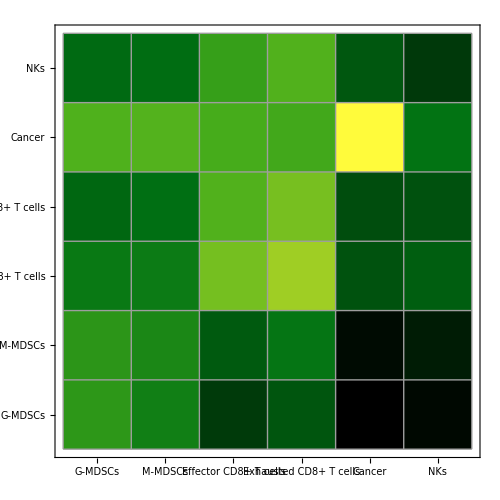
{-Graphics-,-Graphics-}

```mathematica
WEPCmat=Reverse@Rest@Union@Flatten@EPCmat[[2;;,2;;]];
{
Row[{MatrixPlot[
Rescale@EPCmat[[2;;,2;;]],
Mesh->True,PlotRangePadding->None,FrameTicks->{{{Range@6,EPCmat[[1,2;;]]}ᵀ,None},{{Range@6,Rotate[#,π/2]&/@EPCmat[[1,2;;]]}ᵀ,None}},ImageSize->500,ColorFunction->"AvocadoColors",ColorFunctionScaling->False,DataReversed->True],BarLegend[{"AvocadoColors",WEPCmat[[{-1,1}]]}]}],
Graph[
Rule@@EPCmat[[1,#+1]]/.x_String:>StringReplace[x,"_"->"\n"]&/@Position[EPCmat[[2;;,2;;]],_?(#>0&)],
VertexSize->.8,VertexLabels->Placed["Name",{.5,.5}],ImageSize->Large,GraphLayout->"CircularEmbedding"]}
```

```mathematica
ct=EPCmat[[1,2;;]];
sr=Thread[ct->{"G-MDSCs","M-MDSCs","Eff CD8+T","Ex CD8+T","Cancer", "NKs"}]
```

{G-MDSCs→G-MDSCs,M-MDSCs→M-MDSCs,Effector CD8+ T cells→Eff CD8+T,Exhausted CD8+ T cells→Ex CD8+T,Cancer→Cancer,NKs→NKs}

```mathematica
indexPal=2*(Length@ReverseSort[DeleteCases[Flatten[EPCmat⟦2;;,2;;⟧],0]])/3;
indexPal
```

24

```mathematica
TH=ReverseSort[DeleteCases[Flatten[EPCmat⟦2;;,2;;⟧],0]][[indexPal]];
TH
```

0.369612

```mathematica
Total[ReverseSort[DeleteCases[Flatten[EPCmat⟦2;;,2;;⟧],0]][[indexPal;;]]]/Total[ReverseSort[DeleteCases[Flatten[EPCmat⟦2;;,2;;⟧],0]]]
```

0.160528

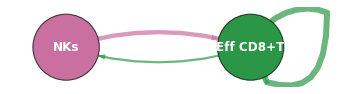

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{1, 2},{1->2,2->1,2-> 2}, VertexLabels->Thread[Range[2]->(Placed[Style[#,12,"Panel",Background->None, Bold, White], Center]&/@{ "NKs","Eff CD8+T"})],VertexSize->0.36,VertexLabelStyle-> Directive[White,Bold, 12],VertexStyle->{1-> RGBColor["#c970a1"], 2-> RGBColor["#2b9746"]},EdgeStyle->{(1 -> 2)-> Directive[Thickness[0.73*0.012], RGBColor["#c970a1"]],(2 -> 1)-> Directive[Thickness[0.37 * 0.012],RGBColor["#2b9746"]],(2 -> 2)-> Directive[Thickness[1* 0.012],RGBColor["#2b9746"]], Arrowheads[Large]},ImageSize->Medium, VertexStyle->GrayLevel@.9,VertexCoordinates->{{0,0},{1,0}}]
```

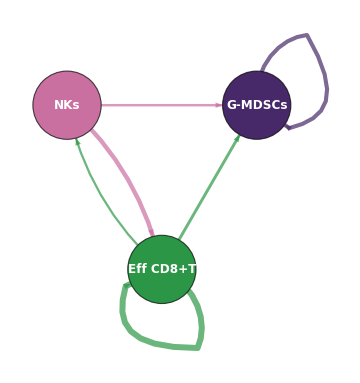

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{1,2,3},{2->1,2->3,3->1, 3->2,1->1, 3-> 3},{FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},ImageSize->Medium,VertexCoordinates->{{Sqrt[3]/2,1},{-1/2*Sqrt[3],1},{0,-1/2}},VertexLabels->Thread[Range[3]->(Placed[Style[#,12,"Panel",Background->None, Bold, White], Center]&/@{ "G-MDSCs",  "NKs","Eff CD8+T"})],
VertexStyle->{2-> RGBColor["#c970a1"], 1 -> RGBColor["#472969"],3-> RGBColor["#2b9746"]},EdgeStyle->{(2 -> 1)-> Directive[Thickness[0.41 * 0.012],RGBColor["#c970a1"]],
(2 -> 3)-> Directive[Thickness[0.73 * 0.012],RGBColor["#c970a1"]],
(1->1) -> Directive[Thickness[0.68 * 0.012],RGBColor["#472969"]],
(3 -> 1)-> Directive[Thickness[0.49* 0.012],RGBColor["#2b9746"]],
(3 -> 2)-> Directive[Thickness[0.37* 0.012],RGBColor["#2b9746"]],
(3->3)-> Directive[Thickness[1 * 0.012],RGBColor["#2b9746"]],  Arrowheads[Large]},
VertexSize->{0.36}}]
```

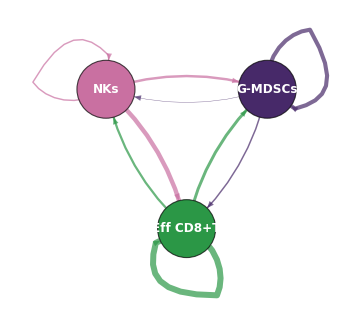

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{1,2,3},{1->1, 1->2, 1->3,2->1,2->2, 2->3,3->1, 3->2, 3-> 3},{FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},ImageSize->Medium,VertexCoordinates->{{Sqrt[3]/2,1},{-1/2*Sqrt[3],1},{0,-1/2}},VertexLabels->Thread[Range[3]->(Placed[Style[#,12,"Panel",Background->None, Bold, White], Center]&/@{ "G-MDSCs",  "NKs","Eff CD8+T"})],
VertexStyle->{2-> RGBColor["#c970a1"], 1 -> RGBColor["#472969"],3-> RGBColor["#2b9746"]},EdgeStyle->{
(1->1) -> Directive[Thickness[0.68 * 0.012],RGBColor["#472969"]],
(1->2) -> Directive[Thickness[ 0.07 * 0.012],RGBColor["#472969"]],
(1 -> 3)->  Directive[Thickness[0.25* 0.012],RGBColor["#472969"]],
(2 -> 1)-> Directive[Thickness[0.41 * 0.012],RGBColor["#c970a1"]],
(2->2)-> Directive[Thickness[0.24 * 0.012],RGBColor["#c970a1"]], 
(2->3)-> Directive[Thickness[0.73 * 0.012],RGBColor["#c970a1"]], 
(3 -> 1)-> Directive[Thickness[0.49* 0.012],RGBColor["#2b9746"]],
(3 -> 2)-> Directive[Thickness[0.37 * 0.012],RGBColor["#2b9746"]],
(3->3)-> Directive[Thickness[1 * 0.012],RGBColor["#2b9746"]],  Arrowheads[Large]},
VertexSize->{0.36}}]
```

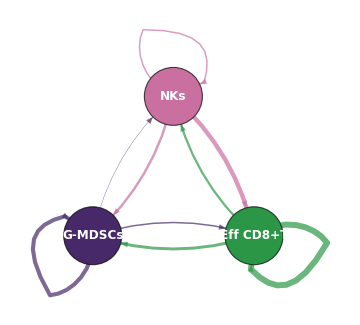

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{1,2,3},{1->1, 1->2, 1->3,2->1,2->2, 2->3,3->1, 3->2, 3-> 3},{FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},ImageSize->Medium,VertexCoordinates->{{-1/2*Sqrt[3],-1}, {0,1/2},{Sqrt[3]/2,-1}},VertexLabels->Thread[Range[3]->(Placed[Style[#,12,"Panel",Background->None, Bold, White], Center]&/@{ "G-MDSCs",  "NKs","Eff CD8+T"})],
VertexStyle->{2-> RGBColor["#c970a1"], 1 -> RGBColor["#472969"],3-> RGBColor["#2b9746"]},EdgeStyle->{
(1->1) -> Directive[Thickness[0.68 * 0.012],RGBColor["#472969"]],
(1->2) -> Directive[Thickness[ 0.07 * 0.012],RGBColor["#472969"]],
(1 -> 3)->  Directive[Thickness[0.25* 0.012],RGBColor["#472969"]],
(2 -> 1)-> Directive[Thickness[0.41 * 0.012],RGBColor["#c970a1"]],
(2->2)-> Directive[Thickness[0.24 * 0.012],RGBColor["#c970a1"]], 
(2->3)-> Directive[Thickness[0.73 * 0.012],RGBColor["#c970a1"]], 
(3 -> 1)-> Directive[Thickness[0.49* 0.012],RGBColor["#2b9746"]],
(3 -> 2)-> Directive[Thickness[0.37 * 0.012],RGBColor["#2b9746"]],
(3->3)-> Directive[Thickness[1 * 0.012],RGBColor["#2b9746"]],  Arrowheads[Large]},
VertexSize->{0.36}}]
```

## PC strength circuits

```mathematica
PCmat=Import["/Users/yingtongliu/Documents/research/CC-model_weight_mat/PC_strength_mat.txt","Table"]
TableForm[PCmat]
```

{{ ,G-MDSCs,M-MDSCs,Effector CD8+ T cells,Exhausted CD8+ T cells,Cancer,NKs},{G-MDSCs,0.955789,0.81055,0.580384,0.612527,0.0404352,0.103766},{M-MDSCs,0.886973,0.774864,0.649231,0.64901,0.0651258,0.098971},{Effector CD8+ T cells,0.638992,0.714054,1.93624,1.79168,0.28394,0.40617},{Exhausted CD8+ T cells,0.589582,0.68137,1.99367,1.79215,0.23756,0.493017},{Cancer,0.776814,0.726972,1.05865,1.2267,0.586285,0.341264},{NKs,0.582984,0.623688,1.26422,1.28937,0.265529,0.288343}}

| G-MDSCs | M-MDSCs | Effector CD8+ T cells | Exhausted CD8+ T cells | Cancer | NKs
G-MDSCs | 0.955789 | 0.81055 | 0.580384 | 0.612527 | 0.0404352 | 0.103766
M-MDSCs | 0.886973 | 0.774864 | 0.649231 | 0.64901 | 0.0651258 | 0.098971
Effector CD8+ T cells | 0.638992 | 0.714054 | 1.93624 | 1.79168 | 0.28394 | 0.40617
Exhausted CD8+ T cells | 0.589582 | 0.68137 | 1.99367 | 1.79215 | 0.23756 | 0.493017
Cancer | 0.776814 | 0.726972 | 1.05865 | 1.2267 | 0.586285 | 0.341264
NKs | 0.582984 | 0.623688 | 1.26422 | 1.28937 | 0.265529 | 0.288343

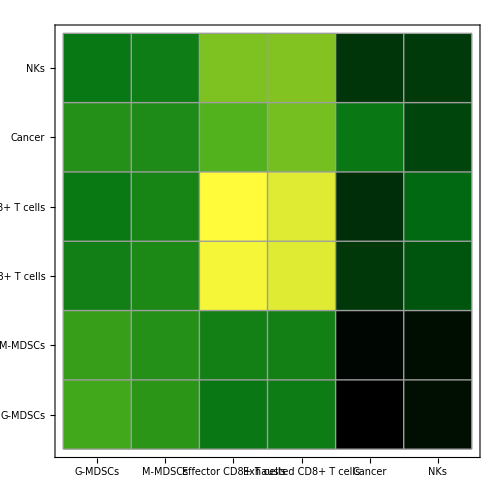
{-Graphics-,-Graphics-}

```mathematica
WPCmat=Reverse@Rest@Union@Flatten@PCmat[[2;;,2;;]];
{
Row[{MatrixPlot[
Rescale@PCmat[[2;;,2;;]],
Mesh->True,PlotRangePadding->None,FrameTicks->{{{Range@6,PCmat[[1,2;;]]}ᵀ,None},{{Range@6,Rotate[#,π/2]&/@PCmat[[1,2;;]]}ᵀ,None}},ImageSize->500,ColorFunction->"AvocadoColors",ColorFunctionScaling->False,DataReversed->True],BarLegend[{"AvocadoColors",WPCmat[[{-1,1}]]}]}],
Graph[
Rule@@PCmat[[1,#+1]]/.x_String:>StringReplace[x,"_"->"\n"]&/@Position[PCmat[[2;;,2;;]],_?(#>0&)],
VertexSize->.8,VertexLabels->Placed["Name",{.5,.5}],ImageSize->Large,GraphLayout->"CircularEmbedding"]}
```

```mathematica
ct=PCmat[[1,2;;]];
sr=Thread[ct->{"G-MDSCs","M-MDSCs","Eff CD8+T","Ex CD8+T","Cancer", "NKs"}]
```

{G-MDSCs→G-MDSCs,M-MDSCs→M-MDSCs,Effector CD8+ T cells→Eff CD8+T,Exhausted CD8+ T cells→Ex CD8+T,Cancer→Cancer,NKs→NKs}

```mathematica
indexPal=Ceiling[2*(Length@ReverseSort[DeleteCases[Flatten[PCmat⟦2;;,2;;⟧],0]])/3];
indexPal
```

24

```mathematica
TH=ReverseSort[DeleteCases[Flatten[PCmat⟦2;;,2;;⟧],0]][[indexPal]];
TH
```

0.582984

```mathematica
Total[ReverseSort[DeleteCases[Flatten[PCmat⟦2;;,2;;⟧],0]][[indexPal;;]]]/Total[ReverseSort[DeleteCases[Flatten[PCmat⟦2;;,2;;⟧],0]]]
```

0.141235

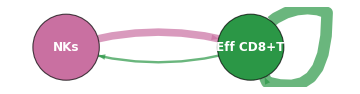

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{1, 2},{1->2,2->1,2-> 2}, VertexLabels->Thread[Range[2]->(Placed[Style[#,12,"Panel",Background->None, Bold, White], Center]&/@{ "NKs","Eff CD8+T"})],VertexSize->0.36,VertexLabelStyle-> Directive[White,Bold, 12],VertexStyle->{1-> RGBColor["#c970a1"], 2-> RGBColor["#2b9746"]},EdgeStyle->{(1 -> 2)-> Directive[Thickness[1.26*0.012], RGBColor["#c970a1"]],(2 -> 1)-> Directive[Thickness[0.4 * 0.012],RGBColor["#2b9746"]],(2 -> 2)-> Directive[Thickness[1.93* 0.012],RGBColor["#2b9746"]], Arrowheads[Large]},ImageSize->Medium, VertexStyle->GrayLevel@.9,VertexCoordinates->{{0,0},{1,0}}]
```

```mathematica
Graph[{1,2,3},{1->3, 2->1,2->3,3->1, 3->2,1->1, 3-> 3},{FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},ImageSize->Medium,VertexCoordinates->{{Sqrt[3]/2,1},{-1/2*Sqrt[3],1},{0,-1/2}},VertexLabels->Thread[Range[3]->(Placed[Style[#,12,"Panel",Background->None, Bold, White], Center]&/@{ "G-MDSCs",  "NKs","Eff CD8+T"})],
VertexStyle->{2-> RGBColor["#c970a1"], 1 -> RGBColor["#472969"],3-> RGBColor["#2b9746"]},EdgeStyle->{(1->3) -> Directive[Thickness[0.58 * 0.012],RGBColor["#472969"]],
(2 -> 1)-> Directive[Thickness[0.58 * 0.012],RGBColor["#c970a1"]],
(2 -> 3)-> Directive[Thickness[1.26 * 0.012],RGBColor["#c970a1"]],
(1->1) -> Directive[Thickness[0.96 * 0.012],RGBColor["#472969"]],
(3 -> 1)-> Directive[Thickness[0.63* 0.012],RGBColor["#2b9746"]],
(3 -> 2)-> Directive[Thickness[0.406* 0.012],RGBColor["#2b9746"]],
(3->3)-> Directive[Thickness[1.93 * 0.012],RGBColor["#2b9746"]],  Arrowheads[Large]},
VertexSize->{0.36}}]
```

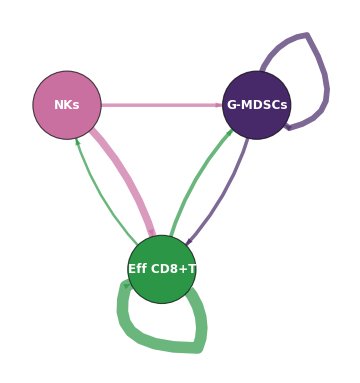
### 

Set::write: Tag Inherited in Inherited[State] is Protected.

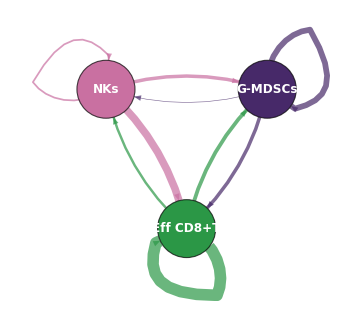

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{1,2,3},{1->1, 1->2, 1->3,2->1,2->2, 2->3,3->1, 3->2, 3-> 3},{FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},ImageSize->Medium,VertexCoordinates->{{Sqrt[3]/2,1},{-1/2*Sqrt[3],1},{0,-1/2}},VertexLabels->Thread[Range[3]->(Placed[Style[#,12,"Panel",Background->None, Bold, White], Center]&/@{ "G-MDSCs",  "NKs","Eff CD8+T"})],
VertexStyle->{2-> RGBColor["#c970a1"], 1 -> RGBColor["#472969"],3-> RGBColor["#2b9746"]},EdgeStyle->{
(1->1) -> Directive[Thickness[0.96 * 0.012],RGBColor["#472969"]],
(1->2) -> Directive[Thickness[ 0.1 * 0.012],RGBColor["#472969"]],
(1 -> 3)->  Directive[Thickness[0.58* 0.012],RGBColor["#472969"]],
(2 -> 1)-> Directive[Thickness[0.58 * 0.012],RGBColor["#c970a1"]],
(2->2)-> Directive[Thickness[ 0.29* 0.012],RGBColor["#c970a1"]], 
(2->3)-> Directive[Thickness[1.26 * 0.012],RGBColor["#c970a1"]], 
(3 -> 1)-> Directive[Thickness[0.63* 0.012],RGBColor["#2b9746"]],
(3 -> 2)-> Directive[Thickness[0.406 * 0.012],RGBColor["#2b9746"]],
(3->3)-> Directive[Thickness[1.93 * 0.012],RGBColor["#2b9746"]],  Arrowheads[Large]},
VertexSize->{0.36}}]
```

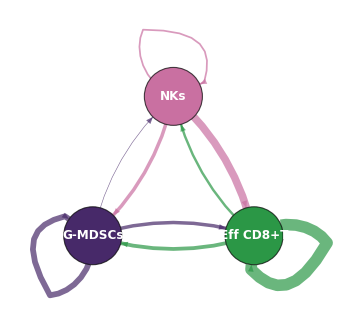

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{1,2,3},{1->1, 1->2, 1->3,2->1,2->2, 2->3,3->1, 3->2, 3-> 3},{FormatType->TraditionalForm,GraphLayout->{"Dimension"->2},ImageSize->Medium,VertexCoordinates->{{-1/2*Sqrt[3],-1}, {0,1/2},{Sqrt[3]/2,-1}},VertexLabels->Thread[Range[3]->(Placed[Style[#,12,"Panel",Background->None, Bold, White], Center]&/@{ "G-MDSCs",  "NKs","Eff CD8+T"})],
VertexStyle->{2-> RGBColor["#c970a1"], 1 -> RGBColor["#472969"],3-> RGBColor["#2b9746"]},EdgeStyle->{
(1->1) -> Directive[Thickness[0.96 * 0.012],RGBColor["#472969"]],
(1->2) -> Directive[Thickness[ 0.1 * 0.012],RGBColor["#472969"]],
(1 -> 3)->  Directive[Thickness[0.58* 0.012],RGBColor["#472969"]],
(2 -> 1)-> Directive[Thickness[0.58 * 0.012],RGBColor["#c970a1"]],
(2->2)-> Directive[Thickness[ 0.29* 0.012],RGBColor["#c970a1"]], 
(2->3)-> Directive[Thickness[1.26 * 0.012],RGBColor["#c970a1"]], 
(3 -> 1)-> Directive[Thickness[0.63* 0.012],RGBColor["#2b9746"]],
(3 -> 2)-> Directive[Thickness[0.406 * 0.012],RGBColor["#2b9746"]],
(3->3)-> Directive[Thickness[1.93 * 0.012],RGBColor["#2b9746"]],  Arrowheads[Large]},
VertexSize->{0.36}}]
```